```mathematica
R=1;
m=0.5(*1.0;*)
L=0;
n=20;
d=20.0; (* total depth of all channels *)
c=.5; (* coupling*)
delta=0.00; (* minimum closed threshold *)
shifts=RandomReal[{0,d/10},n];
vdiag=-d+shifts;
eth=delta+shifts;
(*vdiag[[n]]=-d;
eth[[n]]=0.0;*)
nc=n-1;
io=n;
(* drawing psi grid *)
xi=0;
xf=1.5 R;
ks=√(2 m (d+c))/(2 π) ; (* deepest wave number *)
xx=(xf-xi)ks 12;
nx=xx-Mod[xx,1];
dx=(xf-xi)/(nx-1);
xmat=Table[dx i,{i,nx}];
Do[If[xmat[[i]]<R,itran=i],{i,nx}]

(* possible kinetic energy grids *)
(*wmat={-2,1,0,0};
wmat=N[{−5/2, 4/3,−1/12,0}];*)
wmat=N[{−49/18 ,3/2,−3/20,1/90}];

dh=-0.5 /( m dx^2);

np=200; (* number of coupling strenghts tested *)
dp=0.005*c;
pmat=Table[dp i,{i,np}];

nt=nx n;
(*H=Table[0,{i,nt},{j,nt}];*)
Hsp=Table[0,{i,nx},{j,nx}];
Hin=Table[0,{i,n},{j,n}];
Hout=Table[0,{i,n},{j,n}];

Phold=Table[0,{i,np},{j,200}];
Ehold=Table[0,{j,200}];
Elong=Table[{0,0},{i,np 200}];

(*set up the kinetic energy*)
Do[r=xmat[[i]];
Hsp[[i,i]]=dh wmat[[1]]+L (L+1)/(2. m xmat[[i]]^2);;
If[i<nx,Hsp[[i,i+1]]=dh wmat[[2]];Hsp[[i+1,i]]=Hsp[[i,i+1]];];
If[i<nx-1,Hsp[[i,i+2]]=dh wmat[[3]];Hsp[[i+2,i]]=Hsp[[i,i+2]];];
If[i<nx-2,Hsp[[i,i+3]]=dh wmat[[4]];Hsp[[i+3,i]]=Hsp[[i,i+3]];];
,{i,nx}];

Hrad=Table[RandomVariate[NormalDistribution[0,1]],{i,n},{ip,n}];
nt
str1="hcc";str2=ToString[n];str3=".dat";
If[L==0,file=str1<>str2<>str3;
,str4="L";str5=ToString[L];
file=str1<>str2<>str4<>str5<>str3;
];
out=Table[0,{i,n n}];
Do[k=i+n (j-1);
out[[k]]=Hrad[[i,j]];
If[i==j,out[[k]]=-d];
(*Print[k," ",i," ",j," ",out[[k]]," ",Hrad[[i,j]]];*)
,{j,n},{i,n}];
Export[file,out,"Table"]
```

0.5

240.

hcc20.dat

```mathematica
(* estimate filling of H matrix*)
ix=0;Do[If[Hsp[[i,ip]]≠0,ix=ix+1;],{i,nx},{ip,nx}];
iz=0;Do[If[Hrad[[i,ip]]≠0,iz=iz+1;],{i,n},{ip,n}];
fill= iz ix  1.01
iz ix/(nt nt)
vals=Table[0,{i,fill}];
pos=Table[{0,0},{i,fill}];
```

29088.

0.5

```mathematica
start = SessionTime[];
q=0;
iw=np/10;
Do[
c=pmat[[l]];
Do[If[i==io,
Hin[[i,i]]=vdiag[[i]];Hout[[i,i]]=eth[[i]];,
Hin[[i,i]]=vdiag[[i]];Hout[[i,i]]=eth[[i]];]
If[i<n,Hin[[i,i+1]]=c;Hin[[i+1,i]]=Hin[[i,i+1]]];
If[i<n-1,Hin[[i,i+2]]=c/4.0;Hin[[i+2,i]]=Hin[[i,i+2]]];
,{i,n}];
(* Random *)
(*Do[Do[Hin[[i,ip]]=c Hrad[[i,ip]];Hin[[ip,i]]=Hin[[i,ip]];,{i,ip+1,n}],{ip,n}];*)
iz=0;
Do[Do[k=i+nx (j-1);kp=ip+nx (jp-1);
If[i<itran,
a=Hsp[[i,ip]]KroneckerDelta[j,jp]+ Hin[[j,jp]] KroneckerDelta[i,ip];,
a=Hsp[[i,ip]]KroneckerDelta[j,jp] +Hout[[j,jp]]KroneckerDelta[i,ip];]
If[a≠0,
iz=iz+1;pos[[iz]]={k,kp};vals[[iz]]=a;
iz=iz+1;pos[[iz]]={kp,k};vals[[iz]]=a;
];
(*H[[k,kp]]=a;*)
,{i,ip,nx},{j,jp,n}],{ip,nx},{jp,n}];
If[iz>fill,Print[iz]];
pos0=Table[pos[[i]],{i,iz}];
val0=Table[vals[[i]],{i,iz}];
Hspar=SparseArray[pos0->val0];
(*H=Table[0,{i,nt},{ip,nt}];
Do[H[[pos0[[i,1]],pos0[[i,2]]]]=val0[[i]],{i,iz}];*)
eval=Quiet[Eigenvalues[Hspar]];
nb=0;
ihold=Table[0,{i,nt}];
Do[If[eval[[i]]<0,nb=nb+1;ihold[[nb]]=i],{i,nt}];
sval=Table[eval[[ihold[[i]]]],{i,nb}];
Ehold[[l]]=nb;
t2 = SessionTime[];
If[Mod[l,iw]==0,Print[c," ",nb," time/calc=",(t2-start)/l,"s"]];
Do[Phold[[l,i]]=sval[[i]];q=q+1;Elong[[q]]={c,sval[[i]]};,{i,nb}];

,{l,np}];

stop = SessionTime[];
Print["time ",(stop-start)/60,"m"];
str1="bound";str2=ToString[n];str3=".dat";
If[L==0,file=str1<>str2<>str3;
,str4="L";str5=ToString[L];
file=str1<>str2<>str4<>str5<>str3;
];
Export[file,Elong,"Table"]
```

0.05 20 time/calc=0.131634s

0.1 20 time/calc=0.132182s

0.15 20 time/calc=0.1318725s

0.2 20 time/calc=0.1323702s

0.25 20 time/calc=0.1346948s

0.3 20 time/calc=0.1345871s

0.35 20 time/calc=0.1345892s

0.4 20 time/calc=0.1345226s

0.45 20 time/calc=0.1344605s

0.5 20 time/calc=0.1343595s

time 0.447872m

bound20.dat

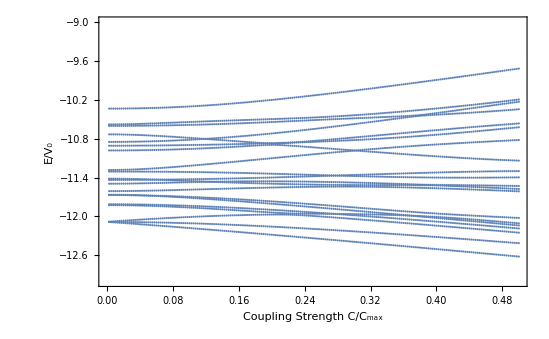

```mathematica
ListPlot[Elong,PlotRange->{-13,-9},Frame->True,LabelStyle->Large,FrameLabel->{"Coupling Strength C/C_max","E/V_0"}]
```

```mathematica
(*iplots={10,30,50,70,90};
nl=Length[iplots];*)
plots=Table[0,{i,np}];
Do[lim=Ehold[[ip]];
short=Table[Phold[[ip,i]],{i,lim}];
sdos=Table[short[[i+1]]-short[[i]],{i,lim-1}];
plots[[ip]]=Histogram[sdos,10];
,{ip,np}]
```

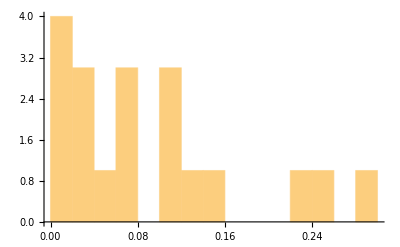

```mathematica
Show[{plots[[10]]}]
```

```mathematica
plots=Table[0,{i,np}];
Do[lim=Ehold[[ip]];
short=Table[Phold[[ip,i]],{i,lim}];
dos=Length[short]/d;
sdos=Table[short[[i+1]]-short[[i]],{i,lim-1}]*dos;
plots[[ip]]=Histogram[sdos,10,"Probability"];
,{ip,np}]
```

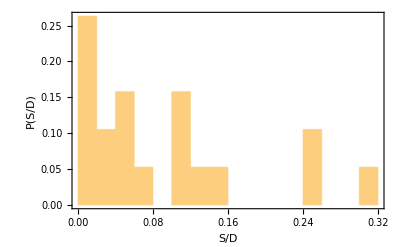

```mathematica
Show[{plots[[1]]},Frame->True,FrameLabel->{"S/D","P(S/D)"},LabelStyle->Medium]
```

```mathematica
(*H=Table[0,{i,nt},{ip,nt}];Do[H[[pos0[[i]]]]=val0[[i]],{i,iz}];
{eval,vec}=Eigensystem[H];
nb=0;
ihold=Table[0,{i,nx}];
Do[If[eval[[i]]<0,nb=nb+1;ihold[[nb]]=i],{i,nt}];
sval=Table[eval[[ihold[[i]]]],{i,nb}];
svec=Table[vec[[ihold[[i]],j]],{i,nb},{j,nt}];
nb
Do[norm=Sqrt[dx Sum[svec[[k,i]]^2 ,{i,nt}]];
Do[svec[[k,i]]=svec[[k,i]]/norm;,{i,nt}];
,{k,1,nb}];*)
```

```mathematica
(*color=Table[Red,{i,n}];color[[io]]=Blue;
it=26;
Plots=Table[0,{k,n}];
Do[short=Table[{xmat[[i]],svec[[it,i+nx (k-1)]]},{i,nx}];
Plots[[k]]=ListPlot[short,Joined->True,PlotStyle->{color[[k]]}];
,{k,n}];
Show[Plots]*)
```